### Define the Parameters

```mathematica
ClearAll[c,λ,ω, k, T, rfAmp, rfFre,rfAmp2,rfFre2, Vpi, V0, Pmax, Pmin,ϵ]
```

ClearAll::ssym: k T rfAmp is not a symbol or a string.

```mathematica
c = 1;(*speed of light m/s*)
λ = 0.01;(*laser wavelength m*)
ω = 2π c/λ; (*angular frequency rad/s*)
k  = 2π/λ; (*wave number*)
T = 2π/ω;(*period*)
rfAmp =4.5;(*RF amplitude in V*)
rfAmp2 =0;(*RF amplitude in V*)
rfFre = 1.437;(*RF frequency in GHz*)
rfFre2= 0.7891;(*RF frequency in GHz*)
ϵ = 1; (*vacuum permittivity*)
Vpi = 3; (*half-wave voltage*)
V0 = 0; (*operation voltage of the EOM (offset)*)
Pmax=1; (*maximum laser power after EOM, mW*)
Pmin= 0 ;(*Pmax/500minimum laser power after EOM, mW*)
```

### Define equations

```mathematica
ClearAll[t,power,Laser, Modulation]
```

```mathematica
Modulation[t_] :=rfAmp Cos[2π rfFre t]+rfAmp2 Cos[2π rfFre2 t];
power[v_]:= Pmin+(Pmax-Pmin)*(0.5Cos[π(v-V0)/Vpi]+0.5);
(*Laser[p_,t_] := Sqrt[Modulation[t]]* Exp[I( ω t-k x)];*)
Laser[p_,t_] := Sqrt[2*p/(c*ϵ)]* Exp[I( ω t-k x)]
```

### Plot the equations

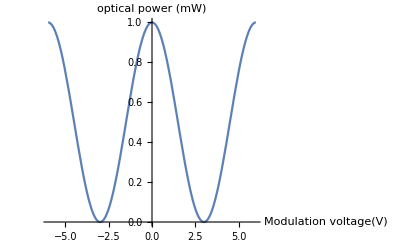

```mathematica
Plot[power[v], {v,-6,6}, AxesLabel->{ "Modulation voltage(V)","optical power (mW)"}]
```

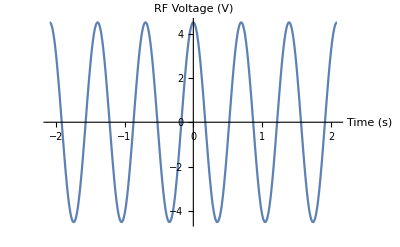

```mathematica
Plot[Modulation[t], {t,-3/rfFre,3/rfFre}, AxesLabel->{ "Time (s)","RF Voltage (V)"}]
```

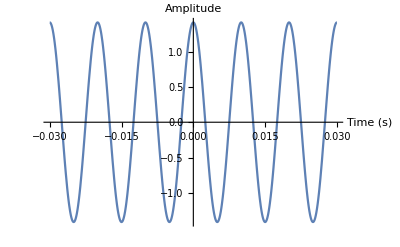

```mathematica
Plot[Re[Laser[1,t]/.{x->0}], {t,-3*2π/ω,3*2π/ω}, AxesLabel->{ "Time (s)","Amplitude"},PlotRange->All]
```

### Apply Modulation to Laser

```mathematica
ClearAll[dt,t,modulatedSignal]
```

```mathematica
t=Table[n,{n,0,5*10^1,5*10^-4}];(*Time array in seconds*)
dt=t[[2]]-t[[1]];(*Time step*)
modulatedSignal = Laser[power[Modulation[t]],t]/.x->0;
```

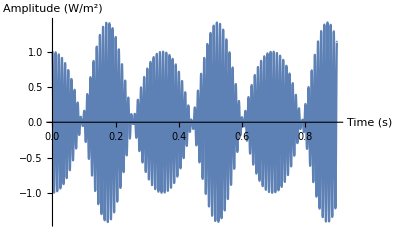

```mathematica
Plot[Re[Laser[power[Modulation[a]],a]]/.x->0,{a,0,9*10^-1} ,AxesLabel->{ "Time (s)","Amplitude (W/m^2)"},PlotRange->All,PlotPoints->2000]
```

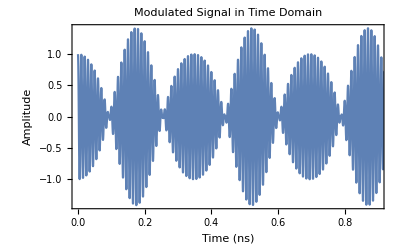

```mathematica
ListLinePlot[Transpose[{t,Re[modulatedSignal]}],PlotRange->{{0,9*10^-1},All},Frame->True,FrameLabel->{"Time (ns)","Amplitude"},PlotLabel->"Modulated Signal in Time Domain"]
```

## Go to the Frequency Space

```mathematica
ClearAll[ftModulatedSignal,frequencies]
```

```mathematica
ftModulatedSignal=Fourier[modulatedSignal,FourierParameters->{-1,-1}]
frequencies=Table[(n-1)/( dt Length[modulatedSignal]),{n,Length[modulatedSignal]}];
```

{5.44438×10^-6+0.0000185476 ⅈ,5.56619×10^-6+0.0000186674 ⅈ,5.45202×10^-6+0.0000188505 ⅈ,5.44141×10^-6+0.0000189959 ⅈ,5.43063×10^-6+0.0000191296 ⅈ,99991,5.4859×10^-6+0.0000175585 ⅈ,5.48083×10^-6+0.0000177877 ⅈ,5.47452×10^-6+0.0000179991 ⅈ,5.46755×10^-6+0.0000181963 ⅈ,5.45815×10^-6+0.0000183818 ⅈ}
 |  |  |  |

```mathematica
f[x_,μ_,FWHM_,height_]:=height/(1+((x-μ)/(FWHM/2))^2)

offset = 100 -23.4891 -1.437;
center1=offset+22.1529;
center2=offset+23.4891;
center3=offset+24.1370;
FWHM=0.100;
height1=0.2;
height2=0.7;
height3=0.3;
A1 = f[frequencies,center1,FWHM,height1];
Ex = f[frequencies,center2,FWHM,height2];
A2 = f[frequencies,center3,FWHM,height3];
NV = A1+Ex+A2;
```

## Plot The Final Results

### Laser and NV Transitions

```mathematica
plotRange =10;(*GHz*)
```

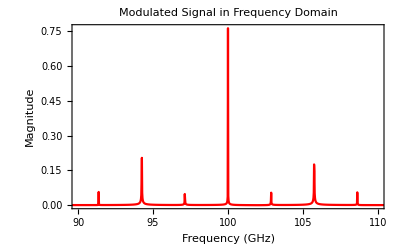

```mathematica
laser=ListLinePlot[Transpose[{frequencies,Abs[ftModulatedSignal]}],PlotRange->{{ω/(2π)-plotRange,ω/(2π)+plotRange},All},Frame->True,FrameLabel->{"Frequency (GHz)","Magnitude"},PlotLabel->"Modulated Signal in Frequency Domain",PlotStyle->Red]
nv =ListLinePlot[Transpose[{frequencies,NV}],PlotRange->{{ω/(2π)-plotRange,ω/(2π)+plotRange},All},Frame->True,FrameLabel->{"Frequency (GHz)","Magnitude"},PlotLabel->"Modulated Signal in Frequency Domain"];
(*Show[laser, nv,PlotRange->{{ω/(2π)-plotRange,ω/(2π)+plotRange},All}]*)
```